```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/WhyMathematica/DataVisualization/bilibili

## BiliData Dashboard

An example of the json api POSTs the data of the form:

{“code”:0,”message”:”0”,”ttl”:1,”data”:{“aid”:1111111,”view”:30673,”danmaku”:231,”reply”:271,”favorite”:519,”coin”:158,”share”:25,”now_rank”:0,”his_rank”:0,”no_reprint”:0,”copyright”:1}}

In this notebook I will fake some data and show off the possible dashboard structure.
The set up of this notebook is definitely NOT optimized for production use or even slightly larger datasets. Python is recommended for the actual data analysis and visualization.

Test Data

```mathematica
scrape[id_]:=Module[{objM},
objM=Import["https://api.bilibili.com/x/web-interface/archive/stat?aid="<>ToString@id,"JSON"];
"data"/.objM
]
```

```mathematica
data=Table[
scrape[i],
{i,10000,11000,10}]/.Null->Sequence[];
```

DataBoard

Data Array

```mathematica
aidA=Replace["aid",data];
favoriteA=Replace["favorite",data];
viewA=Replace["view",data];
shareA=Replace["share",data];
replyA=Replace["reply",data];
danmakuA=Replace["danmaku",data];
coinA=Replace["coin",data];
nrA=Replace["now_rank",data];
hrA=Replace["his_rank",data];
dataA={aidA,favoriteA,viewA,shareA,replyA,danmakuA,coinA,nrA,hrA};
lendataA=Length@dataA;
```

Plot Grid

```mathematica
tabhead={"","aid","favorite","view","share","reply","danmaku","coin","now_rank","his_rank"}
```

{,aid,favorite,view,share,reply,danmaku,coin,now_rank,his_rank}

```mathematica
plts=Table[
ListPlot[
Transpose@{dataA[[i]],dataA[[j]]},PlotStyle->Orange,Frame->True,ImageSize->Medium
],
{i,1,lendataA},{j,1,lendataA}];
pltswh=Prepend[Table[Prepend[plts[[i]],tabhead[[i+1]]],{i,1,lendataA}],Table[tabhead[[i]],{i,1,lendataA+1}]];
```

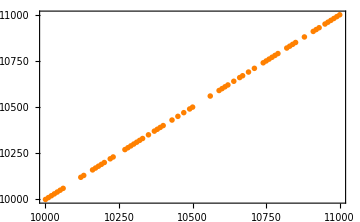
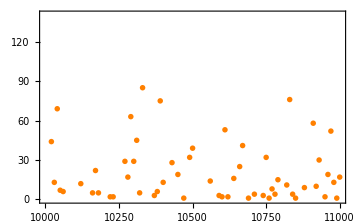
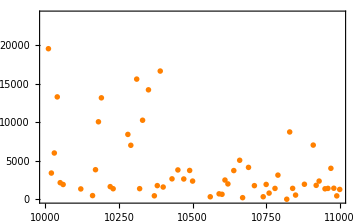
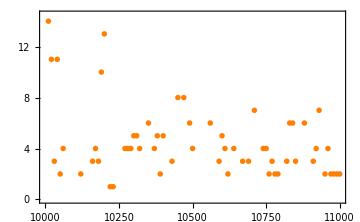
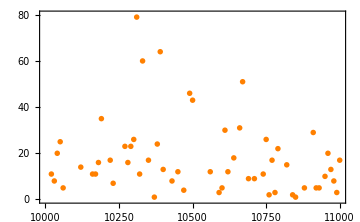
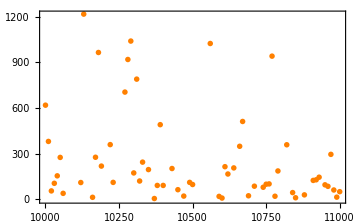
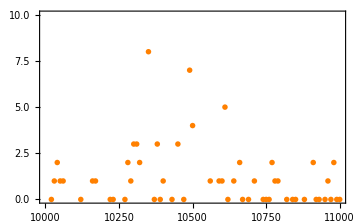
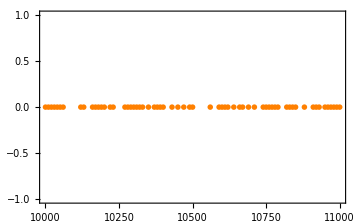
| aid | favorite | view | share | reply | danmaku | coin | now_rank | his_rank
aid | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
favorite | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
view | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
share | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
reply | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
danmaku | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
coin | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
now_rank | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
his_rank | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
pltsg=pltswh//Grid
```

```mathematica
Export["scan-parameters.pdf",pltsg]
Export["scan-parameters.png",pltsg]
```

scan-parameters.pdf

scan-parameters.png